```mathematica
Off[General::munfl,NDSolve::ndsz]
```

```mathematica
Λ=4.0000;
e0=0.5;
C0={-505.1643,-434.958473}[[2]];
μ=938.92/2;hbar=197.327053;
Rmax=60;nGrid=4500;hDif=Rmax/nGrid;
mh2=(μ 2)/(hbar)^2;
Print["μ = ", μ, "     hbarc = ",hbar, "     h^2/2μ = ", N[1/mh2 ]];
```

μ = 469.46     hbarc = 197.327     h^2/2μ = 41.471

## Naive variable-phase method

ℵ) note that this implementation does not work well in the triplet channel where there is a bound state!

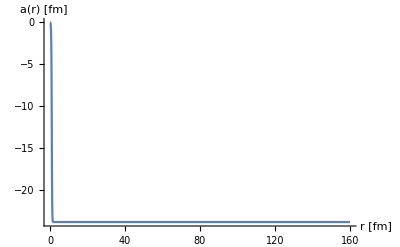
-Graphics- | -Graphics-

```mathematica
v[r_,C0_,Λ_]:=mh2 C0 Exp[- 0.25 r^2 Λ^2];
wf=NDSolve[{w'[r]+w[r]^2-v[r,C0,Λ]==0,w[0.0]==0.0},w,{r,0,Rmax}];
a=NDSolve[{wa'[r]-(r-wa[r])^2 v[r,C0,Λ]==0,wa[0.0]==0.0},wa,{r,0,Rmax}];
Grid[{{Plot[Evaluate[w[x]/.wf],{x,0,Rmax},PlotRange->All,AxesLabel->{"r [fm]","u(r)"}],Plot[Evaluate[wa[x]/.a],{x,0,Rmax},PlotRange->All,AxesLabel->{"r [fm]","a(r) [fm]"}]}}]
```

## Finite (Italian) differences

ℵ) standing-wave boundary conditions: u_0=0 and u_(N+1)=1

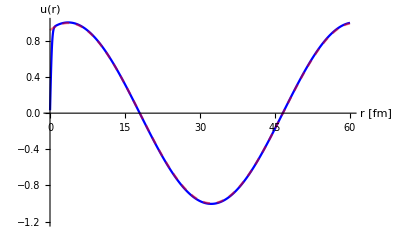

u(x_N) = 0.999862     Δx = 0.0133333 fm      a = -1/ktanδ = -21.4039

```mathematica
Di[i_,h_,ϵ_]:=-2+h^2 mh2 (ϵ-C0 Exp[- Λ^2/4 (i hDif)^2]);
Fi[i_]:=1;

Dmat=DiagonalMatrix[Table[Di[i,hDif,e0],{i,1,nGrid}]];
Fmat=Table[Which[j==i+1,1,j==i-1,1,1==1,0],{i,1,nGrid},{j,1,nGrid}];
bcol=Table[Which[i==nGrid,-1,1==1,0],{i,1,nGrid}];

ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Fmat;
If[nGrid<10,Print[Amat//MatrixForm,"·",ucol//MatrixForm,"=",bcol//MatrixForm]]

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol[[i]]},{i,1,nGrid}];

asywf=nn Sin[Sqrt[2 μ/hbar^2 e0] r+δ];fit=FindFit[wf,asywf,{nn,δ},r];
mod=Function[{r},Evaluate[asywf/.fit]];wfasy2=Table[{i hDif,mod[i hDif]},{i,1,nGrid}];

ListLinePlot[{wf,wfasy2},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,{1.2 Min[usol],Automatic}}]
Print["u(x_N) = ",usol[[-1]],"     Δx = ",N[hDif]," fm      a = -1/ktanδ = ",-(hbar/Sqrt[2 μ e0]) Tan[δ/.fit[[2]]]]
```

ℶ) zero-energy boundary conditions: u_(N+1)=r_(N+1)-a and u_N=r_N-a
     ⇒u_(N+1)=Δr+u_N    and u_0=0

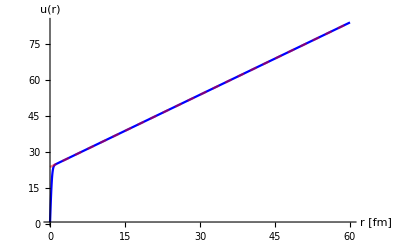

u(x_N) = 83.8268     Δx = 0.0133333 fm      a = r_N-u_N = -23.8268

```mathematica
Dmat=DiagonalMatrix[Table[Di[i,hDif,0],{i,1,nGrid}]];
Fmat=Table[Which[j==i+1,1,j==i-1,1,1==1,0],{i,1,nGrid},{j,1,nGrid}];
bcol=Table[Which[i==nGrid,-hDif,1==1,0],{i,1,nGrid}];
Dmat[[nGrid]][[nGrid]]+=1;

ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Fmat;
If[nGrid<10,Print[Amat//MatrixForm,"·",ucol//MatrixForm,"=",bcol//MatrixForm]]

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol[[i]]},{i,1,nGrid}];
wfasy1=Table[{i hDif,(usol[[-1]]-usol[[-2]]) i+usol[[-2]]-(usol[[-1]]-usol[[-2]]) nGrid},{i,1,nGrid}];

ListLinePlot[{wf,wfasy1},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,{1.2 Min[usol],Automatic}}]
Print["u(x_N) = ",usol[[-1]],"     Δx = ",N[hDif]," fm      a = r_N-u_N = ",Rmax-usol[[-1]]]
```

ℷ) non-local

```mathematica
SolveSecular[Ene_?NumberQ]:=Block[{Asecular,kindisc,wdisc,vdisc,v0disc},
(*iR=R dr^-1;*)
x=Range[iR+1]-1;
(*xFit=0.5;*)
(*Building the matrix: *)
wdisc=Table[W[i*dr,j*dr],{i,0,iR},{j,0,iR}]; 
vdisc=Table[If[i==j,V[i*dr],0],{i,0,iR},{j,0,iR}]; (*The second index is the integrating one (Column number)*)
v0disc=Table[If[i==j≠0,V0[i*dr],0],{i,0,iR},{j,0,iR}]; (*The second index is the integrating one (Column number)*)
kindisc=-h2m/dr^2 SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{iR+1,iR+1}];
Asecular=vdisc+v0disc+wdisc+kindisc;

(*Print[wdisc//MatrixForm];
Print[vdisc//MatrixForm];
Print[v0disc//MatrixForm];
Print[kindisc//MatrixForm];*)

If[Ene==0,
xFit=0.1;
(*are these the correct boundery conditions?*)
boundary=ConstantArray[0,iR+1];
boundary⟦iR+1⟧=-1;
boundary⟦iR⟧=0;
,

xFit=0.5;
FreeWF[ro_,δo_]:=Sin[ro √(Ene/h2m)+δo]/(√(Ene/h2m));
FreeIncoming=Table[FreeWF[i dr,0],{i,0,iR}];
boundary=(vdisc+wdisc).FreeIncoming;


];



(*Solving the system*)
ψu=LinearSolve[Asecular,boundary];
(*ψ=ψ/Max[ψ];*)
ψ=ψu/((ψu⟦iR+1⟧-ψu⟦iR⟧)/dr); (*I divide by the second element to have the derivative in zero = 1*)
(*Fit the longrange behaviour to extract scattering parameters*)
fitarray=Transpose[{dr x[[IntegerPart[iR(xFit)]+2;;iR]],ψ[[IntegerPart[iR(xFit)]+2;;iR]]}];


If[Ene==0,
(* I can use the last 10% of the wavefunction to get slope and intersect *)
AsimptoticWF=Fit[fitarray,{1,r},r];
WF=Transpose[{x*dr,ψ}];
αα=Coefficient[AsimptoticWF,r,0];
ββ=Coefficient[AsimptoticWF,r,1];
a0=-αα/ββ;
WFinterp=Interpolation[WF];
r0=2./αα^2(NIntegrate[(WFinterp[r])^2-(AsimptoticWF)^2,{r,0,R}]);

Print["a = ",a0,"   r0 = ",r0];


,
{Norma,δ}={Normai,δi}/.FindFit[fitarray,Normai FreeWF[r,δi],{Normai,δi},r];
AsimptoticWF[r_]=Norma* FreeWF[r,δ];
WF=Transpose[{x*dr,ψ}];
δ
];
]
```

## Microscopic interaction

```mathematica
δδ[r_]:=Exp[- 0.25 r^2 Λ^2];
Vα0[α0_,r_] :=α0  δδ[r];Vα1[r_] := δδ[r];Vβ1[r_]  :=  r^2 δδ[r];
```

## Fit - Parameter definition

```mathematica
R=1;

Print["a0 = ",Scatt1[R,C0]];
Print[""];
Plot[Scatt1[r,C0],{r,0.4,0.8}]

μ=938.92;hbar=197.327053;
mh2=(μ 2)/(hbar)^2;
h2m=(hbar)^2/(μ 2);
```

μ = 469.46     hbarc = 197.327     h^2/2μ = 41.471

a0 = 1.5877

NDSolve::dsvar: 0.400008 cannot be used as a variable.

Replace::reps: {8.58657+w[0.400008]^2+w'[0.400008]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Replace::argx: Replace called with 2 arguments; 1 argument is expected.

Replace::reps: {8.58657+w[0.400008]^2+w'[0.400008]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Replace::argx: Replace called with 2 arguments; 1 argument is expected.

Replace::reps: {8.58657+w[0.400008]^2+w'[0.400008]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of Replace::reps will be suppressed during this calculation.

Replace::argx: Replace called with 2 arguments; 1 argument is expected.

General::stop: Further output of Replace::argx will be suppressed during this calculation.

NDSolve::dsvar: 0.408171 cannot be used as a variable.

NDSolve::dsvar: 0.416335 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

## Calculation

Definition of the interaction:

My equation:
-h2m ψ’’[r]+V1[r]ψ[r]+Integrate[V2[r,rp]ψ[rp],{rp,0,R}]0

```mathematica
λ=Λ^2/4;
α=1.;
L=0;
C0=-432.1970863199952;
V0[r_]:=(-Ene+h2m(L(L+1))/r^2) ;
V[r_]:=C0 ((2α)/(2α+λ))^(3/2) ⅇ^(-(2α λ)/(2α+λ)r^2);
W[r_,rp_]:=(4π r rp) ( 8 α^(3/2)(h2m(4 α^2 r^2-2 α)+Ene)ⅇ^(-α(rp^2+r^2))-C0(32 √2 α^3)/(2α+λ)^(3/2)ⅇ^(-α(rp^2+(2α+3λ)/(2α+λ)r^2)));


V[r_]:=C0 Exp[- 0.25 r^2 Λ^2];
W[r_,rp_]:=0;
μ=938.92;hbar=197.327053;
mh2=(μ 2)/(hbar)^2;
h2m=(hbar)^2/(μ 2);
```

Definition of the numerical parameters

```mathematica
R=2π / √Ene;
iR=2000;
Λ=4;
λ=Λ^2/4;
L=0;
Ene=0.;
R=50;
dr=R/(iR+1);
```

Solve the equation for zero energy:

```mathematica
SolveSecular[Ene]
```

a = 0.957806   r0 = -0.4218

Set::write: Tag Plus in (-0.957806 + 1.\ r)[r_] is Protected.

```mathematica
AsimptoticWF
```

-0.957806+1. r

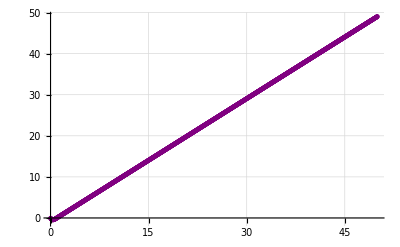

```mathematica
Show[Plot[AsimptoticWF,{r,0,R},PlotStyle->Red,GridLines->Automatic],
ListPlot[WF,PlotStyle->Purple]]
```

Now I do it for many momentums:

a = -421.026   r0 = 605.744

Set::write: Tag Plus in (-20.8669 - 0.0495621\ r)[r_] is Protected.

p = 0.02   R = 314.159  dR = 3.14159   δp = Null

FindMaximum::nrnum: The function value -(-20.8672)[0.] is not a real number at {ro} = {0.}.

FindMaximum::nrnum: The function value -(-21.185)[0.] is not a real number at {ro} = {0.}.

FindMaximum::nrnum: The function value -(-21.5028)[0.] is not a real number at {ro} = {0.}.

General::stop: Further output of FindMaximum :: nrnum will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

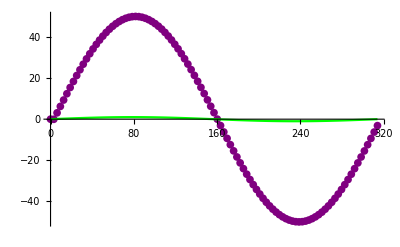

a = -168.41   r0 = 242.298

Set::write: Tag Plus in (-8.34677 - 0.0495621\ r)[r_] is Protected.

p = 0.05   R = 125.664  dR = 1.25664   δp = Null

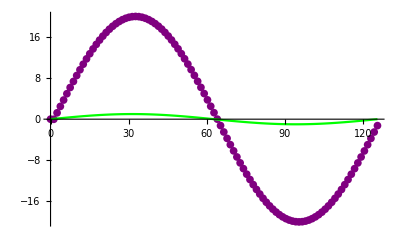

a = -120.293   r0 = 173.07

Set::write: Tag Plus in (-5.96198 - 0.0495621\ r)[r_] is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

p = 0.07   R = 89.7598  dR = 0.897598   δp = Null

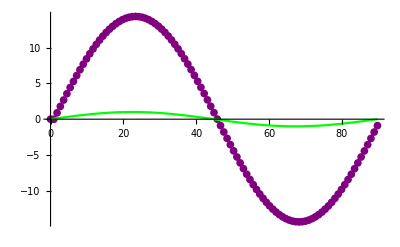

```mathematica
Ps={0.001,0.01,0.1,0.5,1.,2.,5.,7.,10.};
Ps={0.01,0.02,0.05,0.07,0.1,0.2,0.5,0.7,1.,2.,5.,7.,10.,20.,50.,70.,100};
Ps={0.01,0.02,0.05,0.07,0.1,0.2,0.5,0.7,1.,2.};
Ps={0.02,0.05,0.07};
δs={};
Do[
P=Ps⟦i⟧;
Ene=h2m * P^2;
R=2π / P;
iR=100;
dr=R/iR;
δp=SolveSecular[Ene];
δs=Append[δs,δp];
Print["p = ", P, "   R = ",R, "  dR = ", dr, "   δp = ",δp];
Print@Show[
Plot[AsimptoticWF[r]/FindMaximum[AsimptoticWF[ro],{ro,0}]⟦1⟧,{r,0,R},PlotStyle->Red],
ListPlot[WF,PlotStyle->Purple],
Plot[FreeWF[r,0]/FindMaximum[FreeWF[ro,0],{ro,0}]⟦1⟧,{r,0,R},PlotStyle->Green]]
,{i,Length[Ps]}];
```

```mathematica
δs
ERE=Transpose[{Ps,Abs[ Cot[δs]]}];
EREfit=Fit[ERE,{1,y^2,y^4},y]
Show[ListPlot[ERE,PlotStyle->Pink],Plot[EREfit,{y,Min[Ps],Max[Ps]}]]
```

{Null,Null,Null}

1. Abs[Cot[Null]]-1.61035×10^-13 y^2 Abs[Cot[Null]]+7.15966×10^-11 y^4 Abs[Cot[Null]]

-Graphics-

```mathematica
δp
Show[
Plot[AsimptoticWF[r]/FindMaximum[AsimptoticWF[ro],{ro,0}]⟦1⟧,{r,0,R},PlotStyle->Red],
ListPlot[WF,PlotStyle->Purple],
Plot[FreeWF[r,0]/FindMaximum[FreeWF[ro,0],{ro,0}]⟦1⟧,{r,0,R},PlotStyle->Green]]
```

FindMaximum::nrnum: The function value -(-5.96207)[0.] is not a real number at {ro} = {0.}.

FindMaximum::nrnum: The function value -(-6.05286)[0.] is not a real number at {ro} = {0.}.

FindMaximum::nrnum: The function value -(-6.14365)[0.] is not a real number at {ro} = {0.}.

General::stop: Further output of FindMaximum :: nrnum will be suppressed during this calculation.

-Graphics-

```mathematica
(*R=5;
Λ=4;
C0=-432.2107451;
V[r_]:=C0  ⅇ^(-0.25 Λ^2 r^2);
W[r_,rp_]:=0.;
SolveSecular[Ene];
Show[ListPlot[WF],Plot[FreeWF,{r,0,R}]]*)
```